```mathematica
Manipulate[StreamDensityPlot[{-b*x*y+g*y,b*x*y-g*y},{x,0,1},{y,0,1},StreamScale->Large,PlotLabel->Row[{ "b = ",b,", g = ",g,}]],{b,0.0,0.5},{g,0.01,0.2}]
```

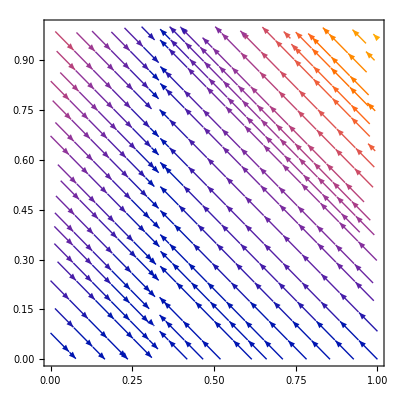

```mathematica
StreamPlot[{-0.3*x*y+0.1*y, 0.3*x*y-0.1*y}, {x,0,1}, {y,0,1}]
```

```mathematica
Show[VectorPlot[{-0.8*x*y+1000*y, 0.8*x*y-1000*y},{x,-1,1001},{y,-1,1001},Epilog->{PointSize[0.02],Point[{x,y}/. First[Solve[{-0.8*x*y+1000*y==0,0.8*x*y-1000*y==0}]]]},Frame->False,Axes->True],ContourPlot[{-0.8*x*y+1000*y==0,0.8*x*y-1000*y==0},{x,-1,1001},{y,-1,1001},ContourStyle->Red]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics-

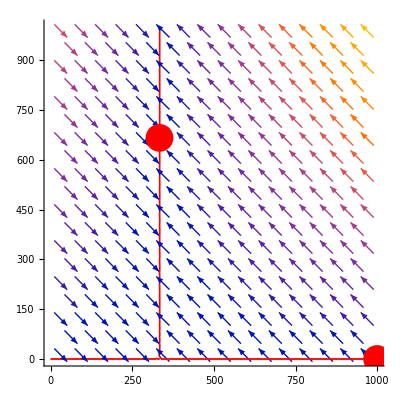

```mathematica
Show[VectorPlot[{-30*x*y+10000*y, 30*x*y-10008*y},{x,-1,1001},{y,-1,1001},Epilog->{{Red, PointSize[0.05],Point[{333,666}]}, {Red, PointSize[0.05], Point[{1000,0}]}},Frame->False,Axes->True],ContourPlot[{-30*x*y+10000*y==0,30*x*y-10000*y==0},{x,-1,1001},{y,-1,1001},ContourStyle->Red, BaseStyle->Thick]]
```

```mathematica
Show[%21,PlotLabel->None,LabelStyle->{24,GrayLevel[0]}]
```

-Graphics-

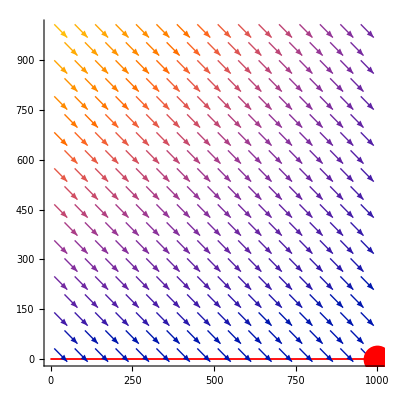

```mathematica
Show[%16,PlotLabel->None,LabelStyle->{24,GrayLevel[0]}]
```

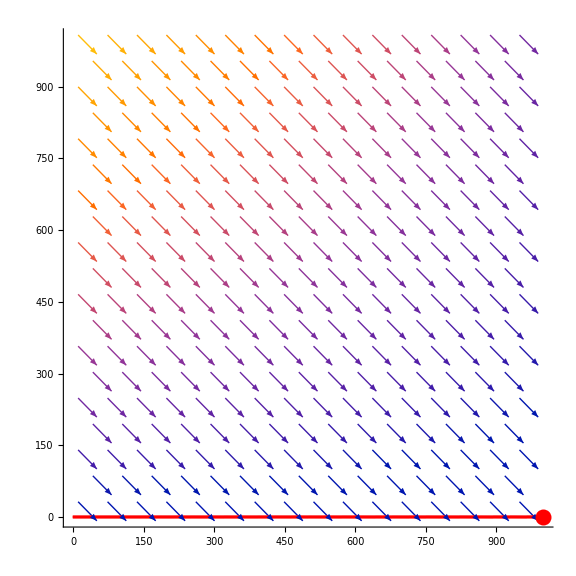

```mathematica
Show[%10,ImageSize->Large]
```

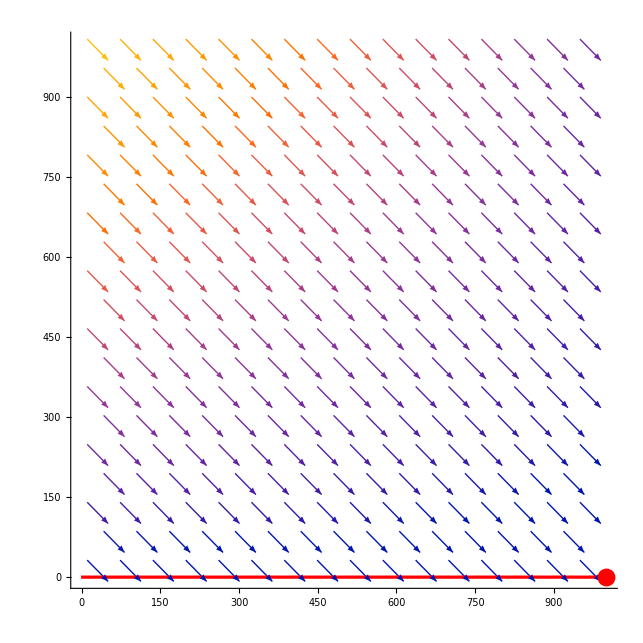

```mathematica
Show[VectorPlot[{-3*x*y+1000*y, 3*x*y-1000*y},{x,-1,1001},{y,-1,1001},ListPlot[{1000,0},{1000/3,2000/3}],Frame->False,Axes->True],ContourPlot[{-3*x*y+1000*y==0,3*x*y-1000*y==0},{x,-1,1001},{y,-1,1001},ContourStyle->Red]]
```

VectorPlot::nonopt: Options expected (instead of ListPlot[{1000,0},{1000/3,2000/3}]) beyond position 3 in VectorPlot[{-3 x y+1000 y,3 x y-1000 y},{x,-1,1001},{y,-1,1001},ListPlot[{1000,0},{1000/3,2000/3}],Frame→False,Axes→True]. An option must be a rule or a list of rules.

Show::gcomb: Could not combine the graphics objects in Show[VectorPlot[{-3 x y+1000 y,3 x y-1000 y},{x,-1,1001},{y,-1,1001},ListPlot[{1000,0},{1000/3,2000/3}],Frame→False,Axes→True],].

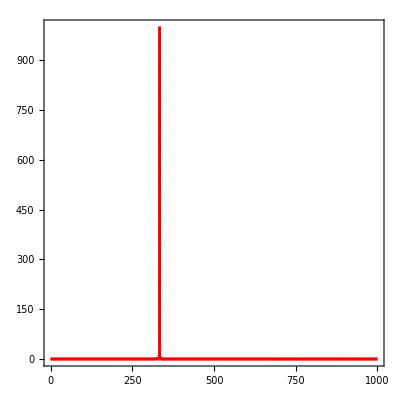
```mathematica
Show[VectorPlot[{-0.8 x y+1000 y,0.8 x y-1000 y},{x,-1,1001},{y,-1,1001},ListPlot[{1000,0}],Frame->False,Axes->True],-Graphics-]
```

VectorPlot::nonopt: Options expected (instead of ListPlot[{1000,0}]) beyond position 3 in VectorPlot[{-0.8 x y+1000 y,0.8 x y-1000 y},{x,-1,1001},{y,-1,1001},ListPlot[{1000,0}],Frame→False,Axes→True]. An option must be a rule or a list of rules.

Show::gcomb: Could not combine the graphics objects in Show[VectorPlot[{-0.8 x y+1000 y,0.8 x y-1000 y},{x,-1,1001},{y,-1,1001},ListPlot[{1000,0}],Frame→False,Axes→True],].

Show[VectorPlot[{-0.8 x y+1000 y,0.8 x y-1000 y},{x,-1,1001},{y,-1,1001},ListPlot[{1000,0}],Frame→False,Axes→True],-Graphics-]

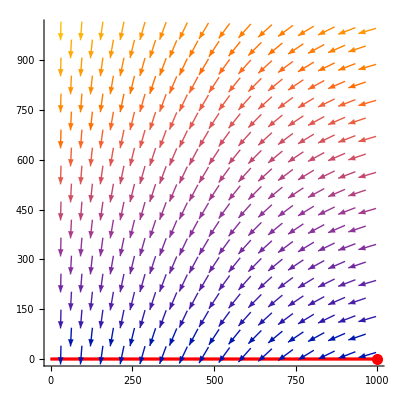

```mathematica
Show[VectorPlot[{-0.8*x*y, 0.8*x*y-1000*y},{x,-1,1001},{y,-1,1001},Epilog->{Red, PointSize[0.02],Point[ {1000, 0}]},Frame->False,Axes->True],ContourPlot[{-0.8*x*y+1000*y==0,0.8*x*y-1000*y==0},{x,-1,1001},{y,-1,1001},ContourStyle->Red]]
```